```mathematica
ClearAll["Global`*"]
```

```mathematica
dx = x[t](1-b- x[t] +b x[t]^2)
```

x[t] (1-b-x[t]+b x[t]^2)

```mathematica
FullSimplify[D[dx,x[t]]/.x[t]->(1-b)/b]
```

```mathematica
Reduce[-3+1/b+2 b<0]
```

b<0||1/2<b<1

```mathematica
sols=Solve[dx/x[t]==0,x[t]]
```

{{x[t]→1},{x[t]→(1-b)/b}}

```mathematica
ys1=x[t]/.sols[[1]]
```

1

```mathematica
ys2=x[t]/.sols[[2]]
```

(1-b)/b

```mathematica
Reduce[ys2>0]
```

0<b<1

```mathematica
V=FullSimplify[r x[t]-1/2  x[t]^2+1/3b x[t]^3-(r s - 1/2  s^2 + 1/3 b s^3)/.{s->ys1,r->1-b}]
```

1/6 (-1+x[t])^2 (-3+4 b+2 b x[t])

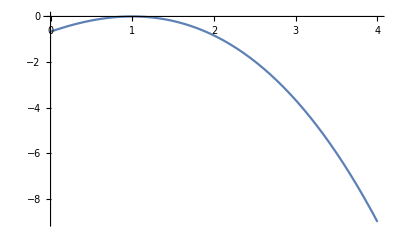

```mathematica
Plot[(V/.b->-1/4),{x[t],0,4}]
```

```mathematica
V2=V/.{x[t]->y}
```

1/6 (-1+y)^2 (-3+4 b+2 b y)

```mathematica
dx2=FullSimplify[dx/.{x[t]->y}/.{r-> 1-b,s->ys1}]
```

(-1+y) y (-1+b+b y)

```mathematica
LF=Collect[3 ExpandAll[W[y]/.FullSimplify[DSolve[W'[y] ==FullSimplify[V2/dx2],W[y],y],Assumptions->y>0][[1]]],{y,Log[y],Log[1-b (1+y)]},FullSimplify]
```

y+3 C[1]+(-2+1/(2-2 b)) Log[y]+((1-2 b)^2 Log[1-b (1+y)])/(2 (-1+b) b)

```mathematica
ExpandAll[(1-2 b)^2/(2 (-1+b) b)]
```

1/(-2 b+2 b^2)-(4 b)/(-2 b+2 b^2)+(4 b^2)/(-2 b+2 b^2)

```mathematica
FullSimplify[1-b (1+y)-(1- 2 b)]
```

b-b y

```mathematica
LF2=Collect[(1+b z2)( y - 1 - Log[y]) + (z2)(b-b y-(1-2b)Log[1-b(1+y)]) /.z2->(-1+2 b)/(2 (-1+b) b),{y,Log[y],Log[1-b(1+y)]},FullSimplify]
```

-1+y+(-2+1/(2-2 b)) Log[y]+1/2 (4+1/(-1+b)-1/b) Log[1-b (1+y)]

```mathematica
FullSimplify[LF-LF2]
```

1+3 C[1]